```mathematica
DSolve[y'[x]==delta* Cos[y[x]],y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→2 ArcTan[Tanh[1/2 (delta x+C[1])]]}}

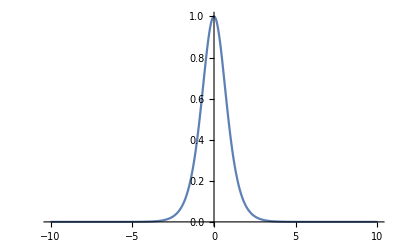

```mathematica
Plot[Cos[2 ArcTan[Tanh[1/2 (x)]]]^2,{x,-10,10},PlotRange->All]
```

```mathematica
<<VariationalMethods`
y[x_]:=2 ArcTan[Tanh[x/(2delta) ]]
VariationalD[(A*z'[x]^2-K*Cos[z[x]]^2-d*z'[x])Cos[y[x]]^2,z[x],x]
```

2 Cos[2 ArcTan[Tanh[x/(2 delta)]]] (K Cos[2 ArcTan[Tanh[x/(2 delta)]]] Cos[z[x]] Sin[z[x]]-(Sech[x/delta] Sin[2 ArcTan[Tanh[x/(2 delta)]]] (d-2 A z'[x]))/delta-A Cos[2 ArcTan[Tanh[x/(2 delta)]]] z''[x])

{{y→InterpolatingFunction[{{-10., 10.}}, <>]}}

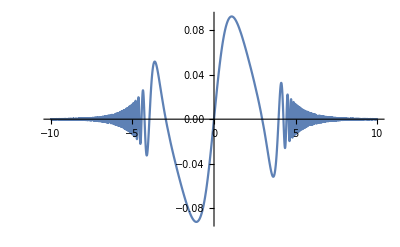

```mathematica
s=NDSolve[{-2Sin[2ArcTan[Tanh[x/2]]](2y'[x]-0.5)+2y''[x]==Sin[2y[x]],y[0]==0,y'[0]==0.15},y,{x,-10,10}]
Plot[Evaluate[Sin[y[x]]Cos[2ArcTan[Tanh[x/2]]]/.s],{x,-10,10},PlotRange->All]
```